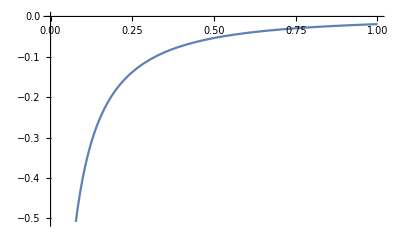

```mathematica
Plot[(-(10. (0.1-0.01 ⅇ^(-10. x)) (1+0.01 x+√(0.1+x)))/(√(0.01 ⅇ^(-10. x)+x))+(1+√(0.01 ⅇ^(-10. x)+x))/(√(0.1+x)))/(2 (1+√(0.01 ⅇ^(-10. x)+x))^2),{x, 0, 1}]
```

```mathematica
ϵ:=.01
```

```mathematica
((1+√(x+ϵ Exp[-10. x]))/(√(0.1+x))-(10. (1+√(0.1+x)+ϵ x) (0.1-ϵ Exp'[-10. x]))/(√(x+ϵ Exp[-10. x])))/(2 (1+√(x+ϵ Exp[-10. x]))^2)
```

```mathematica
(-(10. (0.1-0.01 ⅇ^(-10. x)) (1+0.01 x+√(0.1+x)))/(√(0.01 ⅇ^(-10. x)+x))+(1+√(0.01 ⅇ^(-10. x)+x))/(√(0.1+x)))/(2 (1+√(0.01 ⅇ^(-10. x)+x))^2)
```

-3.45766

```mathematica
x:=0
```

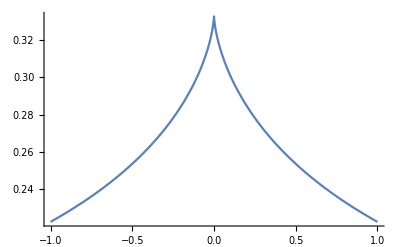

```mathematica
Plot[2/(3(x^2)^(1/3)+6),{x,-1,1}]
```

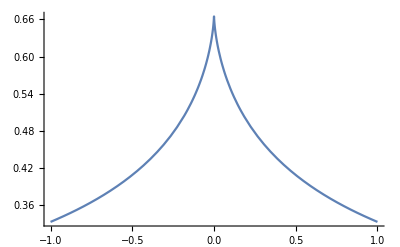

```mathematica
Plot[2/(3(x^2)^(1/3)+3),{x,-1,1}]
```

```mathematica
Solve[y''+x^(1/3)y'=0,y]
```

Set::write: Tag Plus in 0+y'' is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,y]

```mathematica
DSolve[ⅆ/ⅆx ⅆ/ⅆx y+x^(1/3)ⅆ/ⅆx y==0,y,x]
```

```mathematica
DSolve[{x^(1/3) y'[x]+y''[x]==0},y[x],x]
```

DSolve::dsvar: 0 cannot be used as a variable.

DSolve[{y''[0]==0},y[0],0]

```mathematica
y[x]:=3^(1/4)/2^(1/2)c_1 Gamma[3/4,3(ϵ^(-3/4)x)^(4/3)/4]+c_2
```

```mathematica
Simplify[y]
```

y

```mathematica
Simplify[y[x]]
```

3.14038 c_

```mathematica
ξ:=ϵ^(-3/4)x
```

```mathematica
y[x]
```

y[0]

```mathematica
clear
```

clear

```mathematica
Clear[y]
```